```mathematica
h2obasis = {Labeled[57.54,"57.54", Above], 76.56, 88.51};
ch4basis = {72.25, 82.77, 90.89};
c2h4basis = {75.63, 86.69, Labeled[93.17, "93.17", Above]};
h2omp2 = {{.01,0.02361} , {.1,0.10187},{1,4.387}};
ch4mp2={{ .01,0.009890},{ .1,0.5767},{1,1.334}};
c2h4mp2 = {{.01,0.03107},{ .1,0.6000},{ 1,2.510}};
databasis = {h2obasis, ch4basis, c2h4basis};
datamp2 = {h2omp2, ch4mp2, c2h4mp2};
```

```mathematica
databasis[[1,2]]
```

76.5563

```mathematica
chartDatabasis = Table[databasis[[j,i]],{i,1,3},{j,1,3}];
labels = {"ϵ = 0.01", "ϵ = 0.1", "ϵ = 1.0" };
(*chartDatamp2 = Table[datamp2[[j,i]], {i, 1,3}, {j, 1,3}];*)
chartDatamp2 = {h2omp2, ch4mp2, c2h4mp2};
```

```mathematica
colors={Brown,Red,Orange,Green,Yellow,LightBlue};coloredTextures=MapThread[Function[{elem,c},ImageApply[List@@Blend[{Black,c},#]&,elem]],{textures,colors}];
```

MapThread::mptd: Object textures at position {2, 1} in … has only 0 of required 1 dimensions.

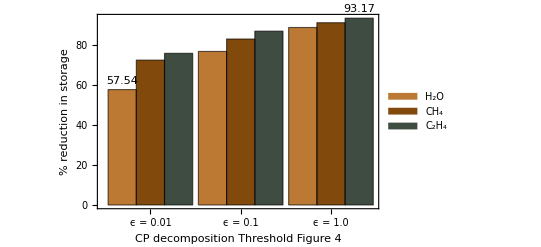

```mathematica
BarChart[chartDatabasis,ChartLabels->{labels,Placed[{"","",""},Above]},BarSpacing->None,FrameLabel->{{"% reduction in storage",None},{"CP decomposition Threshold\n Figure 4",None}},ChartLegends->Placed[{"H_2O", "CH_4" ,"C_2H_4"}, Below],
BaseStyle->{FontFamily->"Arial",FontSize->15},ChartStyle->ColorData[41],
Frame->{{True,None},{True,None}}, PerformanceGoal->"Quality", ColorFunction->{Blue, Orange, Green}(*LabelingFunction->(Placed[#,Above]&)*)]
```

```mathematica
BarChart[chartDatamp2,ChartLabels->{labels,Placed[{"","",""},Above]},BarSpacing->{0.01,.5},FrameLabel->{{"% Error in MP2 Energy",None},{"CP decomposition Threshold",None}},ChartLegends->{"H_2O", "CH_4" ,"C_2H_4"},
BaseStyle->{FontFamily->"Arial",FontSize->15},
Frame->{{True,None},{True,None}}, PerformanceGoal->"Quality"(*, LabelingFunction->(Placed[#,Above]&)*)]
```

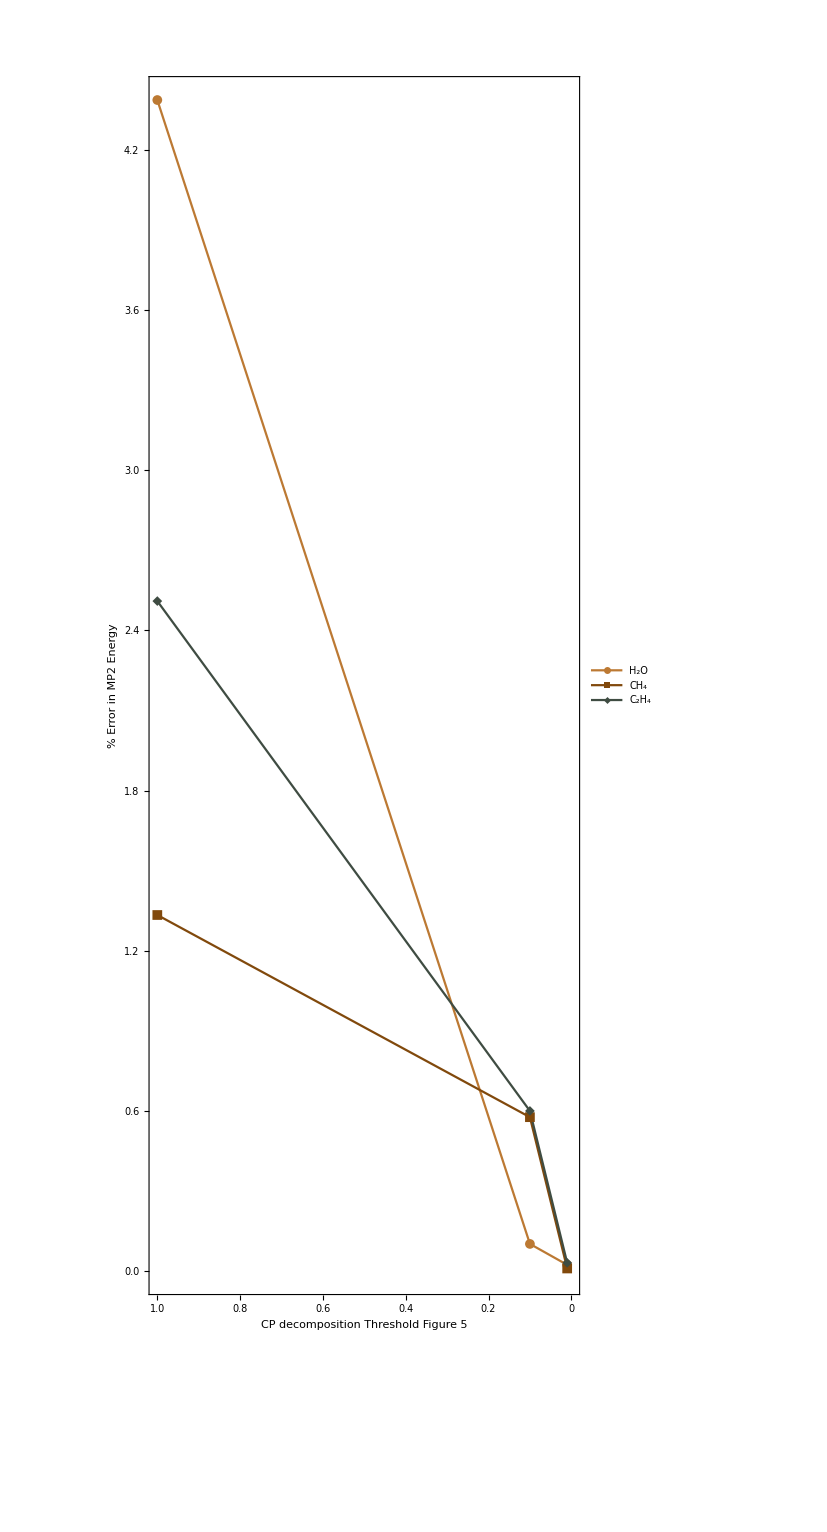

```mathematica
ListLinePlot[chartDatamp2,PlotStyle->41,AxesOrigin->{0,0}, AspectRatio->Full, InterpolationOrder->1, PlotRange->All,PlotLegends->Placed[{"H_2O","CH_4", "C_2H_4"}, {.6,.7}], PlotMarkers->{Automatic, 10}, ScalingFunctions->{"Reverse", None}, Joined->True, FrameLabel->{{"% Error in MP2 Energy",None},{"CP decomposition Threshold\nFigure 5",None}},Frame->{{True,None},{True,None}},BaseStyle->{FontFamily->"Arial",FontSize->15}, PerformanceGoal->"Quality"]
```